## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames[[i]]]]

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

#### variables

```mathematica
begin=350;end=14898;average=0.03;
```

Manipulate[ListPlot[data[n], PlotRange -> {0.95, 1.05}], {n, 0, 22, 1}]

#### Samples

Reflexion GK 300-8000

```mathematica
rgk=Table[ListPlot[data[n],PlotStyle->Blue],{n,7,10,1}];
```

Reflexion TQ 1000-15000

```mathematica
rtq=Table[ListPlot[data[n],PlotStyle->Red],{n,15,18,1}];
```

Transmission GK 300-8000

```mathematica
tgk=Table[ListPlot[data[n],PlotStyle->Darker[Blue]],{n,11,14,1}];
```

Reflexion TQ 1000-15000

```mathematica
ttq=Table[ListPlot[data[n],PlotStyle->Darker[Red]],{n,19,22,1}];
```

#### Composed Plots of both sources

```mathematica
Manipulate[Show[{rgk⟦im⟧,rtq⟦im⟧}],{im,1,4,1},{e,0.1,10}]
```

#### Connect functions

```mathematica
fctab=Table[Interpolation[ExponentialMovingAverage[data[n],average],InterpolationOrder->1],{n,1,Length[fnames]-1}];
```

```mathematica
fct[n_,cut_,x_:x]:=Piecewise[{{fctab⟦n⟧[x], x<cut}, {fctab⟦n+8⟧[x], x>cut}}]
```

```mathematica
Manipulate[Plot[{fctab⟦n⟧[x],fctab⟦n+8⟧[x],fct[n,cut,x]},{x,500,12000},PlotRange->Full],{n,0,14,1},{cut,1000,10000}];
```

```mathematica
cuts={{7,4100},{8,3930},{9,3200},{10,2100},{11,3000},{12,2200},{13,4000},{14,3000}};
```

## Analysis

#### reflexion and transmission functions

```mathematica
reflex[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,1,4}]⟦n-6⟧
```

```mathematica
trans[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,5,8}]⟦n-6⟧
```

```mathematica
Manipulate[Plot[trans[n,x],{x,450,12000}],{n,7,10,1}];
```

```mathematica
Δrg1=0.0;Δrg2=0.0;
```

```mathematica
(*Reflexion einer idealen Grenzfläche in Abhängigkeit von n und κ*)
rg=((n-1)^2+κ^2)/((n+1)^2+κ^2);
```

```mathematica
(*Absorptionskoeffizient*)
β[ν_]:=4*π*Abs[κ]*ν;
```

```mathematica
transth[ν_]:= ((1-rg)(1-rg)*Exp[-β[ν]*d])/(1-(rg)*(rg)*Exp[-2*β[ν]*d]); 
reflth[ν_]:= rg+(((1-(rg))^2)* (rg)*Exp[-2*β[ν]*d])/(1-(rg)*(rg)*Exp[-2*β[ν]*d]);
```

## Stupid way

#### Analysis of GaAs: semi conducting

```mathematica
d=470*10^-4;sample=7;
```

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol=Table[{ν,FindRoot[{transth[ν]-trans[sample,ν],reflth[ν]-reflex[sample,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,450,14000,4}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsemi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsemi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsemi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of GaAs : n-doted

```mathematica
d=440*10^-4;sample=8;
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν]-trans[sample,ν],reflth[ν]-reflex[sample,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,500,12000,6}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlndot=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientndot=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientndot=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of Si : semi conducting

```mathematica
d=530*10^-4;sample=9;
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν]-trans[sample,ν],reflth[ν]-reflex[sample,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,500,13000,8}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

### Functions

```mathematica
brechzahlFCTsemi=Interpolation[ExponentialMovingAverage[brechzahlsemi,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTsemi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTsemi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
brechzahlFCTndot=Interpolation[ExponentialMovingAverage[brechzahlndot,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTndot=Interpolation[ExponentialMovingAverage[extinktionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTndot=Interpolation[ExponentialMovingAverage[absorptionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
plots={brechzahlFCTsemi,extinktionFCTsemi,brechzahlFCTndot,extinktionFCTndot};
```

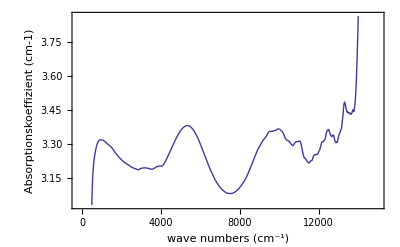
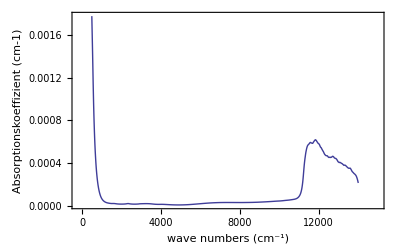
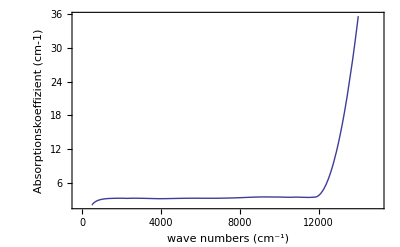
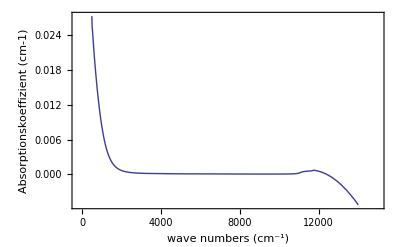

```mathematica
Table[Plot[plots⟦i⟧[x],{x,500,14000},PlotRange->{{-200,15000},Full},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotStyle->Thick,ImageSize->400],{i,1,4}]
```

```mathematica
brechzahlFCTsi=Interpolation[ExponentialMovingAverage[brechzahlsi,average],InterpolationOrder->2];
extinktionFCTsi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsi,average],InterpolationOrder->2];
absorptionFCTsi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsi,average],InterpolationOrder->2];
```

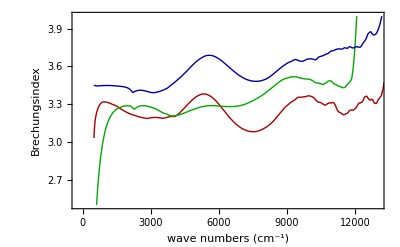

```mathematica
Plot[{brechzahlFCTsemi[x],brechzahlFCTndot[x],brechzahlFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{2.5,4}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Brechungsindex"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

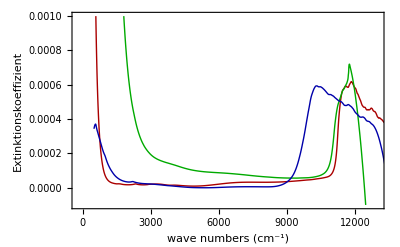

```mathematica
Plot[{extinktionFCTsemi[x],extinktionFCTndot[x],extinktionFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{-0.0001,0.001}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

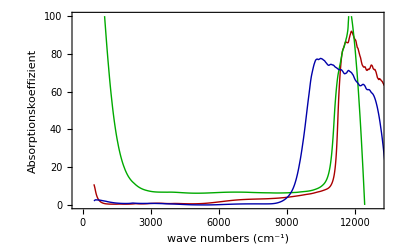

```mathematica
Plot[{absorptionFCTsemi[x],absorptionFCTndot[x],absorptionFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{0,100}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

## proper method

#### general

d = 470*10^-4; sample = 7;sol=.;

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol[sample_,d_]:=Table[{ν,FindRoot[{transth[d,ν]-trans[sample,ν],reflth[d,ν]-reflex[sample,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,500,12000,8}];
```

SetDelayed::write: Tag List in {{500, {n → 3.45157, κ → 0.000343757}}, {508, {n → 3.43906, κ → 0.000347956}}, {516, {n → 3.44423, κ → 0.000356944}}, {524, {n → 3.44656, κ → 0.00035896}}, {532, {n → 3.45235, κ → 0.000354334}}, « 42 », {876, {n → 3.44932, κ → 0.000224276}}, {884, {n → 3.44967, κ → 0.00021905}}, {892, {n → 3.44987, κ → 0.000214508}}, « 1513 »}[sample_, d_] is Protected.

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahl[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,n/.sol[sample,d]⟦j,2⟧⟦1⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizient[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,κ/.sol[sample,d]⟦j,2⟧⟦2⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizient[sample_,d_]:=Table[{sol[sample,d]⟦j,1⟧,4 π sol[sample,d]⟦j,1⟧*κ/.sol[sample,d]⟦j,2⟧⟦2⟧},{j,1,Length[Transpose[sol[sample,d]]⟦1⟧]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

```mathematica
sample[sample_,d_]:={brechzahl[sample,d],extinktionskoeffizient[sample,d],absorptionskoeffizient[sample,d]}
```

SetDelayed::write: Tag Integer in 9[sample_, d_] is Protected.

$Failed

```mathematica
gaasHL=sample[7,470 10^-4]
```

9[7,47/1000]

## freie ladungstraeger

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Clear[ref, βabs]
(*Eingabeparameter*)
Print["Trägerdichte in 10^18 cm^-3"]
ne = 1.05
Print["Streuzeit in 10^-12 s"]
τ = 0.1
Print["relative effektive Masse"]
meff = 0.067
Print["relative Dielektrizitätskonstante"]
ϵ∞ = 3.22^2
Print["LO Phononenfrequenz in cm-1"]
νLO = 292
Print["TO Phononenfrequenz in cm-1"]
νTO = 268
Print["Phononendämpfungskonstante in cm-1"]
Γ = 2.5

```mathematica
Clear[ref, βabs,ext,brec,ϵps,σ]
ϵ∞=3.22^2;
νLO=292;
νTO=268;
Γ=2.5;
```

```mathematica
(*Hochfrequenzleitfähigkeit in (Ωm)-1*)
σ[ne_,τ_,meff_]:=28202.2 (ne*τ)/meff 1/(1-I*0.188364*ν*τ);
(*Dielektrizitätsfunktion,x=Skalierungsfaktor für Gitterbeitrag*)
ϵps[x_,ne_,τ_,meff_]:=ϵ∞(1+x*(νLO^2-νTO^2)/(νTO^2-ν^2-I*ν*Γ))+I σ[ne,τ,meff]/(1.66818*ν);

(*Extinktionskoeffizient*)
ext[x_,ne_,τ_,meff_]:=Im[Sqrt[ϵps[x,ne,τ,meff]]];

(*Brechzahl*)
brec[x_,ne_,τ_,meff_]:=Re[Sqrt[ϵps[x,ne,τ,meff]]];

(*Absorptionskoeffizient*)
βabs[x_,ne_,τ_,meff_]:=4*π*ext[x,ne,τ,meff]*ν;
```

Print["Plasmafrequenz in cm-1"]
νp = 299.48 Sqrt[ne/(meff*ϵ∞)]

Print["Frequenz der oberen Plasmon-Phonon-Mode in cm-1"]
νpp = Sqrt[1/2 (νLO^2 + νp^2) + 1/2 Sqrt[(νLO^2 + νp^2)^2 - 4*νp^2*νTO^2]]

Print["Frequenz der unteren Plasmon-Phonon-Mode in cm-1"]
νpm = Sqrt[1/2 (νLO^2 + νp^2) - 1/2 Sqrt[(νLO^2 + νp^2)^2 - 4*νp^2*νTO^2]]

```mathematica
(*Reflexion am Halbraum*)
rh[x_,ne_,τ_,meff_]:= Abs[(Sqrt[ϵps[x,ne,τ,meff]] - 1)/(Sqrt[ϵps[x,ne,τ,meff]] + 1)]^2;
```

```mathematica
(*Reflexion einer planparallelen Schicht*)
ref[x_,d_,ne_,τ_,meff_]:=rh[x,ne,τ,meff] (1+Exp[-2*βabs[x,ne,τ,meff]*d]-2*rh[x,ne,τ,meff]*Exp[-2*βabs[x,ne,τ,meff]*d])/(1-(rh[x,ne,τ,meff]^2)*Exp[-2*βabs[x,ne,τ,meff]*d]);
```

```mathematica
βexp=absorptionFCTndot;
reflint[ν_]:=reflex[8,ν]
```

```mathematica
(*Einfluss der Schichtdicke d,ohne Gitterbeitrag*)
Manipulate[Plot[{rh[0],0.01+ref[0,640*10^-4,ne,τ,meff],0.02+ref[0,440*10^-4,ne,τ,meff],0.03+ref[0,240*10^-4,ne,τ,meff]},{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"half space","R+0.01,640 µm","R+0.02,440 µm","R+0.03,240 µm"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) ohne Gitterbeitrag "],{ne,1.00,2.00,0.1},{τ,0.1,0.001},{meff,0.03,0.09}]
```

```mathematica
(*Einfluss der Schichtdicke d,mit Gitterbeitrag*)
Plot[{rh[1],0.01+ref[1,640*10^-4],0.02+ref[1,440*10^-4],0.03+ref[1,240*10^-4]},{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"half space","R+0.01,640 µm","R+0.02,440 µm","R+0.03,240 µm"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag "]
```

-Graphics-

```mathematica
(*Vergleich des Experiments mit der Theorie (mit Gitterbeitrag)*)
Manipulate[Plot[{ref[1,640*10^-4,ne,τ,meff],reflint[ν]},{ν,450,2800},PlotRange->{{0,3000},{0,0.5}},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"theory, 440 µm","experiment"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag ",ImageSize->800],{ne,1.00,2.00,0.1},{τ,0.1,0.001},{meff,0.03,0.09}]
```

```mathematica
Plot[{ref[1,640*10^-4]},{ν,110,2800},PlotRange->{{0,3000},{0,0.5}},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"theory, 440 µm","experiment"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag ",ImageSize->800]
```

-Graphics-

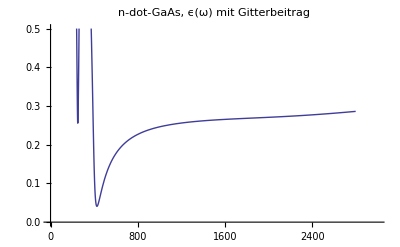

-Graphics-

Exponent der Wellenlängenabhängigkeit von β

3.1

InterpolatingFunction::dmval: Input value {14284.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

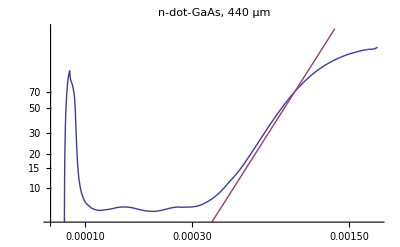

```mathematica
(*Exponent der Wellenlängenabhängigkeit des Absorptionskoeffizienten*)
Print["Exponent der Wellenlängenabhängigkeit von β"]
exponent=3.1
LogLogPlot[{βexp[ν]/.ν->1/λ,2.25*10^11*λ^exponent},{λ,0.002,0.00007},FrameLabel->{"wave length (cm)","Absorptionskoeffizient (cm^-1)"},PlotRange->{5,250},PlotLabel->"n-dot-GaAs,
 440 µm"]
```

```mathematica
(*Darstellung der optischen Konstanten*)

(*Realteil von ϵ,Vergleich mit und ohne Gitterbeitrag*)
Plot[{Re[ϵps[1]],Re[ϵps[0]]},{ν,0.1,2000},PlotRange->{-20,20},FrameLabel->{"wave numbers (cm^-1)","Re(ϵ)"},PlotLabel->"n-dot-GaAs,
 440 µm",PlotLegend->{"mit Gitterbeitrag","ohne Gitterbeitrag"},LegendPosition->{1,-0.3},LegendShadow->{0,0}]

(*Imaginärteil von ϵ,Vergleich mit und ohne Gitterbeitrag*)
Plot[{Im[ϵps[1]],Im[ϵps[0]]},{ν,0.1,2000},PlotRange->{-1,20},FrameLabel->{"wave numbers (cm^-1)","Im(ϵ)"},PlotLabel->"n-dot-GaAs,
 440 µm",PlotLegend->{"mit Gitterbeitrag","ohne Gitterbeitrag"},LegendPosition->{1,-0.3},LegendShadow->{0,0}]

(*Brechzahl,Vergleich mit und ohne Gitterbeitrag*)
Plot[{brec[1],brec[0]},{ν,0.1,2000},PlotRange->{0,5},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotLabel->"n-dot-GaAs,
 440 µm",PlotLegend->{"mit Gitterbeitrag","ohne Gitterbeitrag"},LegendPosition->{1,-0.3},LegendShadow->{0,0}]

(*Extinktionskoeffizient,Vergleich mit und ohne Gitterbeitrag*)
Plot[{ext[1],ext[0]},{ν,0.1,2000},PlotRange->{0,20},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotLabel->"n-dot-GaAs, 440 µm",PlotLegend->{"mit Gitterbeitrag","ohne Gitterbeitrag"},LegendPosition->{1,-0.3},LegendShadow->{0,0}]

(*Absorptionskoeffizient,Vergleich mit und ohne Gitterbeitrag*)
Plot[{βabs[1],βabs[0]},{ν,0.1,2000},PlotRange->{0,20000},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotLabel->"n-dot-GaAs, 440 µm",PlotLegend->{"mit Gitterbeitrag","ohne Gitterbeitrag"},LegendPosition->{1,-0.3},LegendShadow->{0,0}]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»